#### Investigation of Theorem 1.1 of PROCEEDINGS OF THE AMERICAN MATHEMATICAL SOCIETY Volume 125, Number 1, January 1997, Pages 17 {26 S 0002 - 9939 (97) 03930 - 0 ON 2 D PACKINGS OF CUBES IN THE TORUS ANDREW V.REZTSOV AND IAN H.SLOAN

```mathematica
n:=Floor[x Floor[x]]
```

```mathematica
d:=n/x^2
```

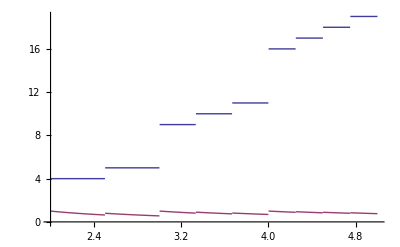

```mathematica
Plot[{n,d},{x,2,5}]
```

Many of these answers are wrong!

```mathematica
Table[{i,Maximize[{d,n==i,x>2},x]},{i,2,20}]
```

{{2,{-∞,{x→Indeterminate}}},{3,{-∞,{x→Indeterminate}}},{4,{1,{x→2}}},{5,{4/5,{x→5/2}}},{6,{-∞,{x→Indeterminate}}},{7,{-∞,{x→Indeterminate}}},{8,{-∞,{x→Indeterminate}}},{9,{1,{x→3}}},{10,{9/10,{x→10/3}}},{11,{9/11,{x→11/3}}},{12,{-∞,{x→Indeterminate}}},{13,{-∞,{x→Indeterminate}}},{14,{-∞,{x→Indeterminate}}},{15,{-∞,{x→Indeterminate}}},{16,{1,{x→4}}},{17,{16/17,{x→17/4}}},{18,{8/9,{x→9/2}}},{19,{16/19,{x→19/4}}},{20,{-∞,{x→Indeterminate}}}}

```mathematica
Table[{i,Maximize[{d,n==i,x>2},x]},{i,24,24}]
```

Maximize::infeas: There are no values of {x} for which the constraints Floor[x\ Floor[x]] == 24 && x > 2 are satisfied and the objective function Floor[x\ Floor[x]]/x^2 is real valued.

{{24,{-∞,{x→Indeterminate}}}}